# Computing for Mathematical Physics

## Exercises 8: Differential Equations

```mathematica
Clear["Global`*"]
```

Click on the line above and press ⇧+⌤ to restart the exercises with any previously held definitions cleared from the memory.

Alternatively, one can restart the Mathematica kernel, which has the same effect, by selecting Evaluation→Quit Kernel→Local from the drop-down menu. Another way to quit the kernel is to type Quit[] in an input cell and then evaluate it by pressing ⇧+⌤.

You are encouraged to use Mathematica's built-in help in the course of these exercises.

## Handy Keyboard Shortcuts

In the longer term, you will certainly find it more efficient to learn at least a few very useful keyboard short-cuts, to avoid having to use the mouse and palettes. Short-cuts for superscript, square-root, pi, ⅇ, and ∞ are especially useful (next subsection).

The material in the subsections below is purely intended as a help, and it contains no questions.

### Frequently used mathematical notation

To use the palette and mouse to enter things like superscripts, integrals, etc, go to the drop-down menu at the top of the screen and select Palettes → Basic Math Assistant .

While it's fine to use the palettes to help enter expressions, particularly on meeting Mathematica for the first time(s), many people find it much more useful and faster in the long-run to be able to enter everything from the keyboard, without any need to go to the mouse.

Some frequently used quick keyboard formulations are shown in the grey box below.
These are generally quite intuitive, and require only a very small investment of time to become fluent in; this pays dividends.

-Graphics-

[Copied from https://reference.wolfram.com/language/tutorial/MathematicalAndOtherNotation.html .]

### Switching from input cells to other cell format types, e.g. text cells

Changing the style of a cell (Input/Text) can be done via the drop-down menu at the top of the screen: Format → Style → Input/Text.

Note that Mathematica only interprets the contents of input cells as code to be processed and run. The contents of text cells is not interpreted as code by Mathematica, and is therefore left as-is. (Aside: one should be careful therefore, when entering code, to be clear that the cell you are working with is indeed an input cell and not a text cell. If in doubt, clicking Format → Style and looking for the ✓ will reveal the currently selected cell’s format type.)

By default, all new cells are input cells. However, writing text cells is essential for communicating the purpose and meaning of code appearing in the input cells to the reader.

Alternatively, the next grey box below shows handy short-key entries for quickly changing the cell style format directly from the keyboard, avoiding the mouse: Alt+7 is especially useful, as it enables us to write text cells like this one, which one will do somewhat frequently later in this course.

Note, on a Mac, you would need to swap the Alt buttons below for ⌘.

-Graphics-

These and further keyboard shortcuts can be found here https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html .

### Greek letters

Entering Greek letters couldn’t really be more easy.
Typically, you just type Esc, then the first letter in the name of the Greek letter you want to print, then Esc again:

-Graphics-
See here for further details: https://reference.wolfram.com/language/tutorial/InputAndOutputInNotebooks.html#14875 .

### Less frequently used mathematical notation

One would typically tend to write the relevant long-hand Mathematica command instead of using the keyboard escape sequences below, for integrals etc.

This is often because, at least in the case of integrals and sums, one often needs to provide Mathematica some helpful assumptions about the nature of parameters appearing in the integrand (real / imaginary / positive / negative / bigger-than-some-other-parameter / ... etc) in order for it to proceed to a meaningful answer.

We only really point these out below as they are fairly intuitive too, despite the caveat above.

-Graphics-

## Repeated operations

### 1. Series solution of the Legendre differential equation

Derive series solutions to the Legendre differential equation 

      • eq. 1:  d/(d x) [ (1-x^2) (d y)/(d x)]-λ y=0 ,

as an expansion about x=0, using terms up to and including O(x^6), for λ=0,-2 and -6.

a) Enter the Legendre differential equation above, storing it as legendreDifferentialEqn.

```mathematica
(* Enter your solution here. *)
legendreDifferentialEqn=D[(1-x^2)D[y[x], x], x]-λ*y[x]==0
```

-λ y[x]-2 x y'[x]+(1-x^2) y''[x]==0

b) Define seriesCoefficients=Table[a[i],{i,0,6}].

```mathematica
(* Enter your solution here. *)
seriesCoefficients = Table[a[i],{i,0,6}]
```

{a[0],a[1],a[2],a[3],a[4],a[5],a[6]}

c) Define a function, seriesSolution[x_], returning a trial series solution of the form, ∑_(i=0)^6 a[i]x^i (cf. the definition of genericSeries[x_] at the start of the lecture notebook).

```mathematica
(* Enter your solution here. *)
seriesSolution[x_]:=SeriesData[x,0, {a[0],a[1],a[2],a[3],a[4],a[5], a[6]},0,7]
seriesSolution[x]
```

a[0]+a[1] x+a[2] x^2+a[3] x^3+a[4] x^4+a[5] x^5+a[6] x^6+O[x]^7

d) Replace y by seriesSolution in legendreDifferentialEqn, saving the result as legendreEqnSeriesSolution.

```mathematica
(* Enter your solution here. *)
legendreEqnSeriesSolution=legendreDifferentialEqn/.y->seriesSolution
```

(-λ a[0]+2 a[2])+(-2 a[1]-λ a[1]+6 a[3]) x+(-6 a[2]-λ a[2]+12 a[4]) x^2+(-12 a[3]-λ a[3]+20 a[5]) x^3+(-20 a[4]-λ a[4]+30 a[6]) x^4+O[x]^5==0

e) Replace λ=0 inside legendreEqnSeriesSolution. Use the resulting equation together with the requirement that the solution must pass through {x,y}={+1,+1}  and  {x,y}={-1,+1}, in order to determine all a[i] (i.e. seriesCoefficients).

```mathematica
(* Enter your solution here. *)
Solve[{
legendreEqnSeriesSolution/.λ->0,
Normal[seriesSolution[x]]==1/.x->1,
Normal [seriesSolution[x]]==1/.x->-1}, seriesCoefficients]
```

{{a[0]→1,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,a[6]→0}}

f) Repeat part e) for λ=-2 instead of  λ=0, replacing the requirement that the function pass through {x,y}={-1,+1}, with the requirement that it pass through {x,y}={-1,-1} instead.

```mathematica
(* Enter your solution here. *)
Solve[{
lambdaminus2Eq =legendreEqnSeriesSolution/.λ->-2 ,
Normal[seriesSolution[x]]==-1/.x->1 ,
 Normal[seriesSolution[x]]==-1 /.x->-1},seriesCoefficients]
```

{{a[0]→15/8,a[1]→0,a[2]→-15/8,a[3]→0,a[4]→-5/8,a[5]→0,a[6]→-3/8}}

g) Repeat part e) for λ=-6 instead of  λ=0.

```mathematica
(* Enter your solution here. *)
Solve[{
legendreEqnSeriesSolution/.λ->-6,
Normal[seriesSolution[x]]==-1/.x->1 ,
 Normal[seriesSolution[x]]==-1 /.x->-1},seriesCoefficients]
```

{{a[0]→1/2,a[1]→0,a[2]→-3/2,a[3]→0,a[4]→0,a[5]→0,a[6]→0}}

### 2. Three atom molecule

The question has basically the same structure as the two-body problem in the lecture notes in section “Simultaneous Differential Equations”.

Three atoms in a molecule interact through forces directed along the lines joining them. With r denoting the appropriate interatomic separation:

• The magnitude of the force between atoms 1 and 2 is :  f(r)=r^-7-r^-4.
• The magnitude of the force between atoms 1 and 3 is :  f(r)=r^-7-r^-4.
• The magnitude of the force between atoms 2 and 3 is :  g(r)=r^-1-1. 

Note that a positive force is repulsive . The atoms lie in the x-y plane. All atoms have unit mass.

The initial positions of the atoms are:
• atom 1 : (0, √3/2)
• atom 2 : (-1/2, 0)
• atom 3 : (1/2, 0).

The initial velocities of the atoms are:
• atom 1 : (0, 0.2)
• atom 2 : (0, -0.1)
• atom 3 : (0, -0.1)

a) Calculate, numerically, the motion of the atoms from time t=0 to 10, according to the following steps.

i)   Code the general form of the  f⃗(r) and g⃗(r) vector functions, as f[i_,j_] and g[i_,j_].

```mathematica
(* Enter your solution here. *)
f[i_,j_]:= Module[{r},
r=Norm[(j-i)];
r^-7-r^-4
]

g[i_,j_]:= Module[{r},
r=Norm[(j-i)];
r^-1-1
]
```

ii)  Define positions vectors for the atoms, r1[t]={x1[t],y1[t]}, etc, to be solved for.

```mathematica
(* Enter your solution here. *)
r1[t_]={x1[t],y1[t]}
r2[t_]={x2[t],y2[t]}
r3[t_]={x3[t],y3[t]}
```

{x1[t],y1[t]}

{x2[t],y2[t]}

{x3[t],y3[t]}

iii) Define the actual force on atom 1 due to atom 2 and atom 3 etc: f12=f⃗(r1,r2),  f13=f⃗(r1,r3), ...

```mathematica
(* Enter your solution here. *)
f12[t] = f[r1[t],r2[t]]*Normalize[r1[t]-r2[t]]
f13[t] = f[r1[t],r3[t]]*Normalize[r1[t]-r3[t]]
f23[t] = g[r2[t],r3[t]]*Normalize[r2[t]-r3[t]]
f32[t] = -f23[t]
f21[t]=-f12[t]
f31[t]=-f13[t]
```

{((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (x1[t]-x2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2)),((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (y1[t]-y2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))}

{((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (x1[t]-x3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2)),((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (y1[t]-y3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2))}

{((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (x2[t]-x3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2)),((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (y2[t]-y3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2))}

{-((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (x2[t]-x3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2)),-((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (y2[t]-y3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2))}

{-((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (x1[t]-x2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2)),-((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (y1[t]-y2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))}

{-((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (x1[t]-x3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2)),-((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (y1[t]-y3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2))}

iv) Define 3 equations of motion (EoMs) to solve of the form m_i(d^2(r⃗)_i)/dt^2=(f⃗)_ij+(f⃗)_ik:
	eq1 = m1 D[r1[t],{t,2}] == f12 + f13  etc

```mathematica
(* Enter your solution here. *)
eq1 = D[r1[t],{t,2}]==f12[t]+f13[t]
eq2 = D[r2[t],{t,2}]== f21[t]+f23[t]
eq3 = D[r3[t],{t,2}] == f31[t]+f32[t]
```

{x1''[t],y1''[t]}=={((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (x1[t]-x2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))+((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (x1[t]-x3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2)),((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (y1[t]-y2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))+((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (y1[t]-y3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2))}

{x2''[t],y2''[t]}=={-((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (x1[t]-x2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))+((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (x2[t]-x3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2)),-((1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^(7/2))-1/((Abs[-x1[t]+x2[t]]^2+Abs[-y1[t]+y2[t]]^2)^2)) (y1[t]-y2[t]))/(√(Abs[x1[t]-x2[t]]^2+Abs[y1[t]-y2[t]]^2))+((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (y2[t]-y3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2))}

{x3''[t],y3''[t]}=={-((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (x1[t]-x3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2))-((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (x2[t]-x3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2)),-((1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^(7/2))-1/((Abs[-x1[t]+x3[t]]^2+Abs[-y1[t]+y3[t]]^2)^2)) (y1[t]-y3[t]))/(√(Abs[x1[t]-x3[t]]^2+Abs[y1[t]-y3[t]]^2))-((-1+1/(√(Abs[-x2[t]+x3[t]]^2+Abs[-y2[t]+y3[t]]^2))) (y2[t]-y3[t]))/(√(Abs[x2[t]-x3[t]]^2+Abs[y2[t]-y3[t]]^2))}

v)  Define 3 initial atom position boundary conditions:
	 r10 = {0,(√3)/2} etc

```mathematica
(* Enter your solution here. *)
r10 = {0, (√3)/2}
r20 = {-1/2,0}
r30 = {1/2,0}
```

{0,(√3)/2}

{-1/2,0}

{1/2,0}

vi) Define 3 initial atom velocity boundary conditions:
 	v10 = {0,1/5} etc

```mathematica
(* Enter your solution here. *)
v10 = {0,0.2}
v20 = {0, -0.1}
v30 = {0, -0.1}
```

{0,0.2}

{0,-0.1}

{0,-0.1}

vii) Feed all the EoMs and boundary conditions to NDSolve and let it do all the hard work

```mathematica
(* Enter your solution here. *)
q3Values=NDSolve[
Join[
Map[
Thread,{eq1,eq2,eq3,r1[0]==r10,r2[0]==r20,r3[0]==r30, (D[r1[t],t]/.t->0)==v10,(D[r2[t],t]/.t->0)==v20,(D[r3[t],t]/.t->0)==v30}]],
Join[r1[t],r2[t],r3[t]], {t,0,10}]
```

{{x1[t]→InterpolatingFunction[…][t],y1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],y2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t],y3[t]→InterpolatingFunction[…][t]}}

b)  ParametricPlot the solutions for the positions of the three atoms (r1[t], r2[t], and r3[t]) as a function of t. You should see that although atom 1 oscillates up and down the y-axis, atoms 2 and 3 execute complicated motions. This is because they started in a superposition of two different normal modes of the molecule, with different frequencies.

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

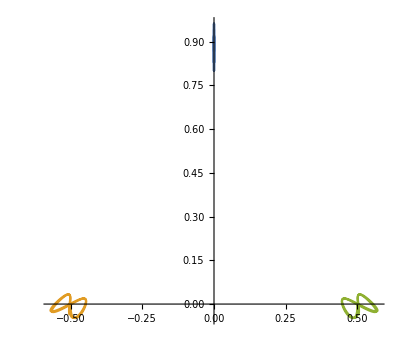

```mathematica
(* Enter your solution here. *)
r1[t_]=Flatten[r1[t]/.q3Values]
r2[t_]=Flatten[r2[t]/.q3Values]
r3[t_]=Flatten[r3[t]/.q3Values]
ParametricPlot[{r1[t],r2[t],r3[t]}, {t,0,10}]
```

c) In a pure bond-stretching mode the initial velocities are changed. Repeat parts a) and b) using these bond-stretching mode initial velocities instead:
• atom 1 : (0, 0.2)
• atom 2 : 0.1(-1/√3, -1)
• atom 3 : 0.1(1/√3, -1)

{{x1[t]→InterpolatingFunction[…][t],y1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],y2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t],y3[t]→InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

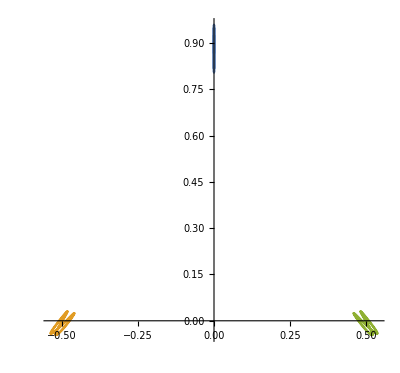

```mathematica
(* Enter your solution here. *)
Clear["Global`*"]
f[i_,j_]:= Module[{r},
r=Norm[(j-i)];
r^-7-r^-4
];

g[i_,j_]:= Module[{r},
r=Norm[(j-i)];
r^-1-1
];
r1[t_]={x1[t],y1[t]};
r2[t_]={x2[t],y2[t]};
r3[t_]={x3[t],y3[t]};
f12[t] = f[r1[t],r2[t]]*Normalize[r1[t]-r2[t]];
f13[t] = f[r1[t],r3[t]]*Normalize[r1[t]-r3[t]];
f23[t] = g[r2[t],r3[t]]*Normalize[r2[t]-r3[t]];
f32[t] = -f23[t];
f21[t]=-f12[t];
f31[t]=-f13[t];
eq1 = D[r1[t],{t,2}]==f12[t]+f13[t];
eq2 = D[r2[t],{t,2}]== f21[t]+f23[t];
eq3 = D[r3[t],{t,2}] == f31[t]+f32[t];
r10 = {0, (√3)/2};
r20 = {-1/2,0};
r30 = {1/2,0};
v10= {0,0.2};
v20 = {-0.1/(√3), -0.1};
v30 = {0.1/(√3),-0.1};
q3Values=NDSolve[
Join[
Map[
Thread,{eq1,eq2,eq3,r1[0]==r10,r2[0]==r20,r3[0]==r30, (D[r1[t],t]/.t->0)==v10,(D[r2[t],t]/.t->0)==v20,(D[r3[t],t]/.t->0)==v30}]],
Join[r1[t],r2[t],r3[t]], {t,0,10}]
r1[t_]=Flatten[r1[t]/.q3Values]
r2[t_]=Flatten[r2[t]/.q3Values]
r3[t_]=Flatten[r3[t]/.q3Values]
ParametricPlot[{r1[t],r2[t],r3[t]}, {t,0,10}]
```

### 3. Shooting method

Use a shooting method, like that described in the last section of this week’s lecture notebook, to find the solution of

       • eq. 2:  y''-x^2 y = x +x^3,

subject to the boundary conditions, y(-1)=0 and y(1)=0. Proceed according to the following steps.

```mathematica
Clear["Global`*"]
```

a) Code eq. 2 in Mathematica, storing it as q3DifferentialEquation.

```mathematica
(* Enter your solution here. *)
q3DifferentialEquation = y''[x]-x^2 y[x]==x+x^3
```

-x^2 y[x]+y''[x]==x+x^3

b) Define a function q3Solver[slopeGuess_]. The function should call NDSolve to return a solution of eq. 2, for the range -1≤x≤1, subject to the boundary conditions  y(-1)=0 and  y'(-1)=slopeGuess.

```mathematica
(* Enter your solution here. *)
q3Solver[slopeGuess_]:= NDSolve[{q3DifferentialEquation, y[-1]==0, y'[-1]==slopeGuess},y[x], {x,-1,1}]
```

c) Define a function yAtxEq1[slopeGuess_?NumericQ], returning the value of the solution output by q3Solver[slopeGuess][[1]] for the point x=1.

```mathematica
(* Enter your solution here. *)
yAtxEq1[slopeGuess_?NumericQ]:= y[x]/.(q3Solver[slopeGuess][[1]])/.x->1
```

d) Evaluate yAtxEq1, manually, inserting guessed-at values for slopeGuess. See how close you can get to having yAtxEq1 output 0, as required by the second true boundary condition in the question, i.e. y(1)=0.

```mathematica
(* Enter your solution here. *)
yAtxEq1[0.5]
yAtxEq1[0.55]
yAtxEq1[0.52]
yAtxEq1[0.51978]
```

-0.0451277

0.0688556

0.000465646

-0.0000358806

e) Use FindRoot with yAtxEq1, to determine, precisely, numerically, the value of y'(-1) leading to a y(x) solution which satisfies y(1)=0. Store this value as q3DesiredSlope.

```mathematica
(* Enter your solution here. *)
q3DesiredSlope =slp/.FindRoot[yAtxEq1[slp]==0,{slp,1} ]
```

0.519796

f) Define a function, q3Solution[x_], by extracting the relevant interpolating function from the output of q3Solver[q3DesiredSlope].  Make a basic plot of q3Solution over the range  -1≤x≤1.

{InterpolatingFunction[…][x]}

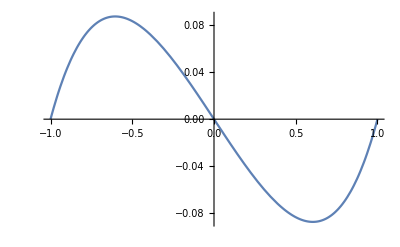

```mathematica
(* Enter your solution here. *)
q3Solution[x_]=y[x]/.q3Solver[q3DesiredSlope]
Plot[q3Solution[x], {x,-1,1}]
```

g) Evaluate the LHS of eq. 2, i.e.  y''-x^2 y, with y(x) replaced by q3Solution[x], storing the result as LHS. Evaluate RHS=x+x^3. Plot LHS  and RHS on the same graph, over the range  -1≤x≤1, to check whether they agree with one another.

{-x^2 InterpolatingFunction[…][x]+InterpolatingFunction[…][x]}

x+x^3

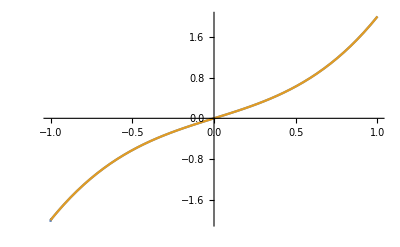

```mathematica
(* Enter your solution here. *)
LHS=D[y[x],{x,2}]-x^2 y[x]/.y->q3Solution
RHS = x+x^3
Plot[{LHS,RHS},{x,-1,1}]
```

### K. Hamilton Last revision 15:35 21 Feb 2023

Part::pspec1: Part specification KeyAbsent is not applicable.

Append::normal: Nonatomic expression expected at position 1 in Append[KeyAbsent,Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1]].

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

Append::argt: Append called with 4 arguments; 1 or 2 arguments are expected.

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Append::argt: Append called with 5 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Append::argt will be suppressed during this calculation.

MapAt::psl: Position specification Append[KeyAbsent,Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],«991»] in … is not a machine-sized integer or a list of machine-sized integers.